# SpinDynamica Tutorial 02: Configuring Flexible 2D Experiments Using HSQC

## Heteronuclear spin selection, coherence pathways, propagation engines, echo and constant-time evolution, channel-dependent sequences, relaxation, and quadrature diagnostics.

## 0. Setup and Loading SpinDynamica

Evaluate both setup cells in order. Cell 1 locates the SpinDynamica repository root upward from NotebookDirectory[] using System` symbols only and loads SpinDynamica`; Cell 2 verifies that Signal2D and Spectrum2D loaded cleanly.

```mathematica
nbRepoRoot=Quiet[Check[NotebookDirectory[],Directory[]]];
While[StringQ[nbRepoRoot]&&nbRepoRoot=!=""&&!FileExistsQ[FileNameJoin[{nbRepoRoot,"SpinDynamica","SpinDynamica.m"}]],With[{parent=ParentDirectory[nbRepoRoot]},If[parent===nbRepoRoot,nbRepoRoot=Directory[];Break[],nbRepoRoot=parent]]];
If[FileExistsQ[FileNameJoin[{nbRepoRoot,"SpinDynamica","SpinDynamica.m"}]],Needs["SpinDynamica`",FileNameJoin[{nbRepoRoot,"SpinDynamica","SpinDynamica.m"}]],Needs["SpinDynamica`"]];
```

SetUserLevel::ini: The user level is being initialized to 2. The user level may be set to an integer between 1 and 3 by using SetUserLevel[level]. Low user levels provide strong syntax trapping at the expense of slow execution for some routines. High user levels relax the syntax trapping in order to provide better execution speeds.

SetUserLevel::ul: The user level has been set to 2.

SetUserLevel::modsymbs: Additional definitions have been given to the following symbols: {Commutator, Duration, Exp, Expand, Plus, Power, Simplify, SolidAngle, Times, WignerD}

```mathematica
{MemberQ[$Packages,"Signals`Signal2D`"],MemberQ[$Packages,"Simulations`Signal2D`"],Context[Signal2D],Context[QuadratureDiagnostics]}
```

{True,True,Simulations`Signal2D`,Signals`Signal2D`}

## 1. Constructing a Heteronuclear HSQC Experiment

Tutorial 01 used a homonuclear two-spin system where both preparation and detection acted identically on all spins. In heteronuclear 2D experiments such as HSQC, different isotopes experience spin-selective RF pulses, evolve under different chemical shifts in t1 and t2, transfer magnetization across a heteronuclear scalar coupling J_HN, and are detected selectively on one spin.

Below we set up a simple two-spin-1/2 {1H, 15N} system with 1H shift +180 Hz, 15N shift -210 Hz, and J_HN = 92 Hz (INEPT delay tau = 1/(4 J_HN)).

```mathematica
SetSpinSystem[{{"1H",1/2},{"15N",1/2}}];
nuH=180.;
nuN=-210.;
jHN=92.;
tauHN=1./(4.*jHN);
Hhn=2.*Pi*(nuH*opI["1H","z"]+nuN*opI["15N","z"]+jHN*(opI["1H","z"].opI["15N","z"]));
```

1         1
SetSpinSystem::set : the spin system has been set to {{1H, -}, {15N, -}}
                                                           2         2

1         1
SetBasis::set : the state basis has been set to ZeemanBasis[{{1H, -}, {15N, -}}, BasisLabels -> Automatic].
                                                                  2         2

We start from proton polarization (InitialDensityOperator -> opI["1H", "z"]), transfer coherence from 1H to 15N with an INEPT Preparation block, refocus 1H-15N coupling in the indirect dimension with Evolution1 -> {"Echo", Pulse["1H", {Pi, "x"}]}, transfer back via a reverse-INEPT Mixing block, and detect only 1H (Observable -> {"1H"}) while encoding quadrature specifically on 15N (QuadratureSpins -> {"15N"}). Notice the spin-selective pulses Pulse["1H", ...], Pulse["15N", ...], and simultaneous Pulse[{"1H", "15N"}, ...].

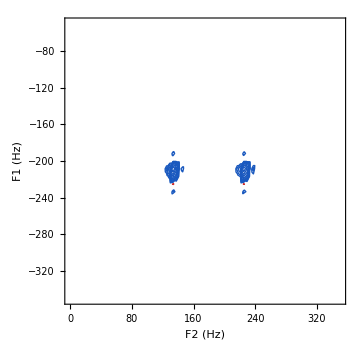

```mathematica
prepHN={Pulse["1H",{Pi/2,"x"}],Delay[tauHN],Pulse[{"1H","15N"},{Pi,"x"}],Delay[tauHN],Pulse["1H",{Pi/2,"y"}],Pulse["15N",{Pi/2,"x"}]};
ev1Echo={"Echo",Pulse["1H",{Pi,"x"}]};
mixConv={Pulse[{"1H","15N"},{Pi/2,"x"}],Delay[tauHN],Pulse[{"1H","15N"},{Pi,"x"}],Delay[tauHN]};
sigHSQC=Signal2D[{{{2Pi800.,48}},{{2Pi800.,96}}},InitialDensityOperator->opI["1H","z"],BackgroundGenerator->Hhn,Preparation->prepHN,Evolution1->ev1Echo,Mixing->mixConv,Observable->{"1H"},QuadratureSpins->{"15N"},QuadratureMethod->"States",LineBroadening->25.];
specHSQC=PhaseSpectrum2D[FT[sigHSQC,ZeroFill->{2,2}],{{-Pi/2,0.},{0.,0.}}];
PlotSpectrum2D[specHSQC,PlotRange->{{0,350},{-350,-50}},ImageSize->360]
```

What to observe: Because Evolution1 refocuses J_HN during t1 while direct acquisition evolves freely, a pure absorptive doublet appears along F2 at nuH +/- J_HN/2 = 134 Hz and 226 Hz, centered at the 15N frequency F1 = -210 Hz.

## 2. QuadratureSpins, QuadratureOrder, and CoherencePathway

In multi-spin systems it is essential to distinguish three related options:
  - QuadratureSpins: specifies WHICH spins receive the indirect quadrature phase shift or coherence filter ({"15N"} in HSQC, rather than All).
  - QuadratureOrder: specifies the positive integer coherence order q scaling the preparation phase step (-Pi/(2q)) and Echo/AntiEcho filters (+/- q).
  - CoherencePathway: applies explicit coherence-order filtration before/after mixing (independent of quadrature encoding, unlike explicit multi-scan PhaseCycle averaging).

In our HSQC, 15N evolves as single-quantum coherence (p1 in {-1, +1}) during t1 and 1H is detected at p2 = -1 after mixing. Adding CoherencePathway -> {{-1, 1}, -1} explicitly enforces this pathway and agrees with the unfiltered HSQC to machine precision.

```mathematica
sigHSQCPath=Signal2D[{{{2Pi800.,48}},{{2Pi800.,96}}},InitialDensityOperator->opI["1H","z"],BackgroundGenerator->Hhn,Preparation->prepHN,Evolution1->ev1Echo,Mixing->mixConv,Observable->{"1H"},QuadratureSpins->{"15N"},QuadratureMethod->"States",CoherencePathway->{{-1,1},-1},LineBroadening->25.];
Max[Abs[sigHSQCPath["Cos"]-sigHSQC["Cos"]]]
```

2.37144×10^-16

As a brief isolated example of higher coherence order on this same two-spin pair, a two-spin double-quantum (q = 2) preparation creates +/-2 coherence spanning BOTH spins (QuadratureSpins -> {"1H", "15N"}). Setting QuadratureOrder -> 2 adjusts the preparation States phase step to -Pi/4, and CoherencePathway -> {{-2, 2}} filters out zero-quantum terms so the indirect peak appears cleanly at the sum frequency nuH + nuN = 180 - 210 = -30 Hz.

```mathematica
prepDQ={Pulse["1H",{Pi/2,"x"}],Delay[2.*tauHN],Pulse["15N",{Pi/2,"x"}]};
mixDQ=Pulse[{"1H","15N"},{Pi/2,"x"}];
sigDQ=Signal2D[{{{2Pi800.,48}},{{2Pi800.,96}}},InitialDensityOperator->opI["1H","z"],BackgroundGenerator->Hhn,Preparation->prepDQ,Mixing->mixDQ,Observable->{"1H"},QuadratureSpins->{"1H","15N"},QuadratureOrder->2,CoherencePathway->{{-2,2}},QuadratureMethod->"States",LineBroadening->25.];
specDQ=FT[sigDQ,ZeroFill->{2,2}];
{"DQ PreparationPhaseShifts"->sigDQ["Metadata"]["PreparationPhaseShifts"],"Peak F1 (Hz) vs nuH + nuN"->{specDQ["Frequency1"][[First[Ordering[Max/@specDQ["HypercomplexMagnitude"],-1]]]],nuH+nuN}}
```

{DQ PreparationPhaseShifts→<|Cos→{0.},Sin→{-0.785398}|>,Peak F1 (Hz) vs nuH + nuN→{-33.3333,-30.}}

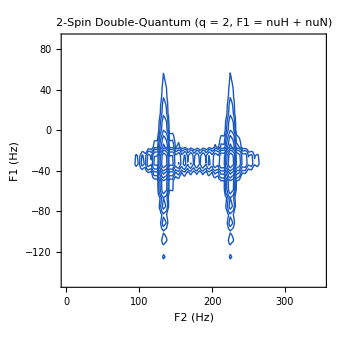

```mathematica
PlotSpectrum2D[specDQ,Component->"HypercomplexMagnitude",PlotRange->{{0,350},{-150,90}},PlotLabel->"2-Spin Double-Quantum (q = 2, F1 = nuH + nuN)",ImageSize->340]
```

## 3. Alternative Propagation Methods (SignalCalculationMethod)

Signal2D provides multiple numerical propagation backends via SignalCalculationMethod:
  - "DoubleDiagonalization" (Automatic default for static liquid-state problems): diagonalizes the indirect and direct generators once and evaluates all (t1, t2) points analytically in the eigenbasis. Usually fastest for ordinary static Hamiltonians and Liouvillians.
  - "SteppedPropagator": precomputes single-step propagators Exp[-I H dt] (and direct eigendecomposition when static) and steps sequentially; handles arbitrary stepped sequences during evolution.
  - "Direct": propagates step-by-step via general SpinDynamica trajectory evaluation; serves as the reference implementation for arbitrary time-dependent problems.
(For periodic time-dependent Hamiltonians such as MAS, Signal2D automatically selects "COMPUTE2D", which is covered in specialized solid-state tutorials.)

Setting ReportSignalCalculationMethod -> True prints which engine and state space (Hilbert vs Liouville) were selected. Here we verify that all three liquid-state engines agree to machine precision.

```mathematica
sigDD=Signal2D[{{{2Pi800.,48}},{{2Pi800.,96}}},InitialDensityOperator->opI["1H","z"],BackgroundGenerator->Hhn,Preparation->prepHN,Evolution1->ev1Echo,Mixing->mixConv,Observable->{"1H"},QuadratureSpins->{"15N"},QuadratureMethod->"States",SignalCalculationMethod->"DoubleDiagonalization",ReportSignalCalculationMethod->True,LineBroadening->25.];
sigStep=Signal2D[{{{2Pi800.,48}},{{2Pi800.,96}}},InitialDensityOperator->opI["1H","z"],BackgroundGenerator->Hhn,Preparation->prepHN,Evolution1->ev1Echo,Mixing->mixConv,Observable->{"1H"},QuadratureSpins->{"15N"},QuadratureMethod->"States",SignalCalculationMethod->"SteppedPropagator",LineBroadening->25.];
sigDir=Signal2D[{{{2Pi800.,48}},{{2Pi800.,96}}},InitialDensityOperator->opI["1H","z"],BackgroundGenerator->Hhn,Preparation->prepHN,Evolution1->ev1Echo,Mixing->mixConv,Observable->{"1H"},QuadratureSpins->{"15N"},QuadratureMethod->"States",SignalCalculationMethod->"Direct",LineBroadening->25.];
{"Max |DD - SteppedPropagator|"->Max[Abs[sigDD["Cos"]-sigStep["Cos"]]],"Max |DD - Direct|"->Max[Abs[sigDD["Cos"]-sigDir["Cos"]]]}
```

Signal2D::reportscm: Using SignalCalculationMethod -> DoubleDiagonalization (Hilbert space).

{Max |DD - SteppedPropagator|→4.80172×10^-15,Max |DD - Direct|→7.96909×10^-15}

## 4. Alternative Indirect Evolution Schemes (Evolution1)

Using the exact same spin system and preparation/mixing blocks, Evolution1 lets you replace free t1 evolution with split refocusing or constant-time schemes:
  1. Evolution1 -> None: conventional free evolution for total time t1; J_HN evolves during t1, splitting the F1 cross peak.
  2. Evolution1 -> {"Echo", refocusEvents}: splits t1 into t1/2 - refocusEvents - t1/2; applying a 180-degree 1H pulse in the middle refocuses J_HN while preserving 15N chemical shift.
  3. Evolution1 -> {"ConstantTime", tCT, refocusEvents}: keeps total indirect duration fixed at tCT via (tCT + t1)/2 - refocus - (tCT - t1)/2 (requiring tCT >= t1_max). Using a simultaneous 180-degree {1H, 15N} pulse keeps J-modulation constant across t1 while encoding 15N shift over t1.

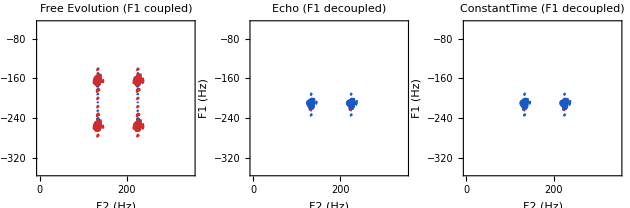

```mathematica
sigFree=Signal2D[{{{2Pi800.,48}},{{2Pi800.,96}}},InitialDensityOperator->opI["1H","z"],BackgroundGenerator->Hhn,Preparation->prepHN,Evolution1->None,Mixing->mixConv,Observable->{"1H"},QuadratureSpins->{"15N"},QuadratureMethod->"States",LineBroadening->25.];
tCT=7./jHN;
sigCT=Signal2D[{{{2Pi800.,48}},{{2Pi800.,96}}},InitialDensityOperator->opI["1H","z"],BackgroundGenerator->Hhn,Preparation->prepHN,Evolution1->{"ConstantTime",tCT,Pulse[{"1H","15N"},{Pi,"x"}]},Mixing->mixConv,Observable->{"1H"},QuadratureSpins->{"15N"},QuadratureMethod->"States",LineBroadening->25.];
spFree=PhaseSpectrum2D[FT[sigFree,ZeroFill->{2,2}],{{-Pi/2,0.},{0.,0.}}];
spCT=PhaseSpectrum2D[FT[sigCT,ZeroFill->{2,2}],{{-Pi/2,0.},{0.,0.}}];
GraphicsRow[{PlotSpectrum2D[spFree,PlotRange->{{0,350},{-350,-50}},PlotLabel->"Free Evolution (F1 coupled)",ImageSize->240],PlotSpectrum2D[specHSQC,PlotRange->{{0,350},{-350,-50}},PlotLabel->"Echo (F1 decoupled)",ImageSize->240],PlotSpectrum2D[spCT,PlotRange->{{0,350},{-350,-50}},PlotLabel->"ConstantTime (F1 decoupled)",ImageSize->240]},Spacings->10]
```

Comparing F1 slices at F2 = 134 Hz makes the J_HN splitting under free evolution vs clean decoupling under both Echo and ConstantTime immediately obvious.

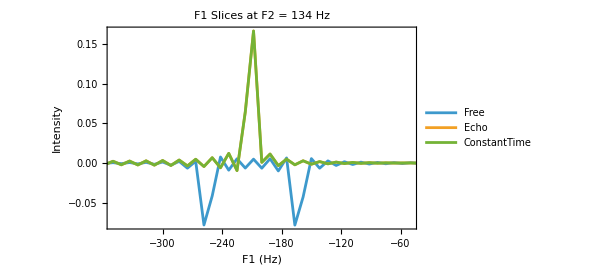

```mathematica
ListLinePlot[{ExtractSlice[spFree,"F1",134.],ExtractSlice[specHSQC,"F1",134.],ExtractSlice[spCT,"F1",134.]},Frame->True,PlotRange->{{-350,-50},All},FrameLabel->{"F1 (Hz)","Intensity"},PlotLegends->{"Free","Echo","ConstantTime"},PlotLabel->"F1 Slices at F2 = 134 Hz",ImageSize->440]
```

## 5. Channel-Dependent Preparation

For standard "States" quadrature, Signal2D automatically rotates the final preparation operator on QuadratureSpins by -Pi/2 around z to build the "Sin" channel from the "Cos" preparation sequence. Alternatively, you can pass an explicit channel Association to Preparation -> <|"Cos" -> ..., "Sin" -> ...|>.

This gives you direct control over individual quadrature channels â.80.94 essential when preparation uses shaped or selective pulses whose phases are programmed per channel rather than rotated abstractly. Changing the final 15N 90-degree pulse phase from "x" to "-y" produces the exact same -Pi/2 z-rotation as automatic "States" encoding.

```mathematica
prepPhase[pN_]:={Pulse["1H",{Pi/2,"x"}],Delay[tauHN],Pulse[{"1H","15N"},{Pi,"x"}],Delay[tauHN],Pulse["1H",{Pi/2,"y"}],Pulse["15N",{Pi/2,pN}]};
sigPrepChan=Signal2D[{{{2Pi800.,48}},{{2Pi800.,96}}},InitialDensityOperator->opI["1H","z"],BackgroundGenerator->Hhn,Preparation-><|"Cos"->prepPhase["x"],"Sin"->prepPhase["-y"]|>,Evolution1->ev1Echo,Mixing->mixConv,Observable->{"1H"},QuadratureSpins->{"15N"},QuadratureMethod->"States",LineBroadening->25.];
{"Max |Explicit Cos - Auto Cos|"->Max[Abs[sigPrepChan["Cos"]-sigHSQC["Cos"]]],"Max |Explicit Sin - Auto Sin|"->Max[Abs[sigPrepChan["Sin"]-sigHSQC["Sin"]]]}
```

{Max |Explicit Cos - Auto Cos|→0.,Max |Explicit Sin - Auto Sin|→2.3066×10^-16}

## 6. Channel-Dependent Mixing

Just like Preparation, Mixing also accepts a channel-dependent Association: <|"Cos" -> ..., "Sin" -> ...|> for States/StatesTPPI/OversampledStates, or <|"Echo" -> ..., "AntiEcho" -> ...|> for EchoAntiEcho. Thus preparation, indirect evolution, and mixing do not have to be identical across quadrature channels.

First, an elementary States association on Mixing (using AutomaticQuadratureEncoding -> True so automatic preparation-side phase shifting remains active):

```mathematica
sigMixStates=Signal2D[{{{2Pi800.,48}},{{2Pi800.,96}}},InitialDensityOperator->opI["1H","z"],BackgroundGenerator->Hhn,Preparation->prepHN,Evolution1->ev1Echo,Mixing-><|"Cos"->mixConv,"Sin"->mixConv|>,Observable->{"1H"},QuadratureSpins->{"15N"},QuadratureMethod->"States",AutomaticQuadratureEncoding->True,LineBroadening->25.];
Max[Abs[sigMixStates["Sin"]-sigHSQC["Sin"]]]
```

0.

A classic NMR application of channel-dependent mixing is sensitivity-enhanced (PEP / Rance-Kay) HSQC under EchoAntiEcho. Whereas conventional reverse-INEPT mixing (mixConv) converts only one of the two orthogonal transverse 15N components after t1, the double-INEPT PEP mixing block (mixPEP) converts both into observable 1H magnetization when paired with opposite 15N pulse phases ("-x" vs "x") for the "Echo" and "AntiEcho" channels, doubling the coherent signal amplitude in a noiseless simulation (corresponding to a Sqrt[2] experimental SNR gain). Note we set AutomaticQuadratureEncoding -> True so automatic Echo/AntiEcho pathway filtering (-1 / +1) stays enabled alongside the channel-dependent Mixing.

```mathematica
mixPEP[pN_]:={Pulse["1H",{Pi/2,"x"}],Pulse["15N",{Pi/2,pN}],Delay[tauHN],Pulse[{"1H","15N"},{Pi,"x"}],Delay[tauHN],Pulse["1H",{Pi/2,"y"}],Pulse["15N",{Pi/2,"y"}],Delay[tauHN],Pulse[{"1H","15N"},{Pi,"x"}],Delay[tauHN],Pulse["1H",{Pi/2,"x"}]};
sigConvEA=Signal2D[{{{2Pi800.,48}},{{2Pi800.,96}}},InitialDensityOperator->opI["1H","z"],BackgroundGenerator->Hhn,Preparation->prepHN,Evolution1->ev1Echo,Mixing->mixConv,Observable->{"1H"},QuadratureSpins->{"15N"},QuadratureMethod->"EchoAntiEcho",LineBroadening->25.];
sigPepEA=Signal2D[{{{2Pi800.,48}},{{2Pi800.,96}}},InitialDensityOperator->opI["1H","z"],BackgroundGenerator->Hhn,Preparation->prepHN,Evolution1->ev1Echo,Mixing-><|"Echo"->mixPEP["x"],"AntiEcho"->mixPEP["-x"]|>,Observable->{"1H"},QuadratureSpins->{"15N"},QuadratureMethod->"EchoAntiEcho",AutomaticQuadratureEncoding->True,LineBroadening->25.];
spConvEA=PhaseSpectrum2D[FT[sigConvEA,ZeroFill->{2,2}],{{-Pi/2,0.},{0.,0.}}];
spPepEA=PhaseSpectrum2D[FT[sigPepEA,ZeroFill->{2,2}],{{-Pi/4,0.},{Pi/4,0.}}];
{"Conv Norms"->QuadratureDiagnostics[sigConvEA]["ChannelNorms"],"PEP Norms"->QuadratureDiagnostics[sigPepEA]["ChannelNorms"],"PEP / Conv HypercomplexMagnitude Ratio"->Max[spPepEA["HypercomplexMagnitude"]]/Max[spConvEA["HypercomplexMagnitude"]]}
```

{Conv Norms→<|Echo→9.96098,AntiEcho→9.96098|>,PEP Norms→<|Echo→1.06977×10^-30,AntiEcho→1.06977×10^-30|>,PEP / Conv HypercomplexMagnitude Ratio→1.07435×10^-31}

## 7. AutomaticQuadratureEncoding (Automatic | True | False)

The final implemented semantics of AutomaticQuadratureEncoding are simple and explicit:
  - Automatic (default): enables automatic preparation-side phase shifts (-Pi/(2q)) and Echo/AntiEcho filters whenever BOTH Preparation and Mixing are channel-independent, and automatically DISABLES them whenever either Preparation or Mixing is a channel Association.
  - True: forces automatic preparation encoding ON even when Mixing is supplied as a channel Association (used in Section 6 above).
  - False: disables all automatic preparation encoding, giving the user full manual control over every channel.

Let us verify all four combinations directly from the resulting Metadata and time-domain channels.

```mathematica
sigAEDefault=sigHSQC;
sigAEAutoMix=Signal2D[{{{2Pi800.,48}},{{2Pi800.,96}}},InitialDensityOperator->opI["1H","z"],BackgroundGenerator->Hhn,Preparation->prepHN,Evolution1->ev1Echo,Mixing-><|"Cos"->mixConv,"Sin"->mixConv|>,Observable->{"1H"},QuadratureSpins->{"15N"},QuadratureMethod->"States",AutomaticQuadratureEncoding->Automatic,LineBroadening->25.];
sigAETrueMix=sigMixStates;
sigAEFalse=Signal2D[{{{2Pi800.,48}},{{2Pi800.,96}}},InitialDensityOperator->opI["1H","z"],BackgroundGenerator->Hhn,Preparation->prepHN,Evolution1->ev1Echo,Mixing->mixConv,Observable->{"1H"},QuadratureSpins->{"15N"},QuadratureMethod->"States",AutomaticQuadratureEncoding->False,LineBroadening->25.];
TableForm[{{"Standard (no Assoc, Automatic)",sigAEDefault["Metadata"]["AutomaticQuadratureEncoding"],sigAEDefault["Metadata"]["PreparationPhaseShifts"],Max[Abs[sigAEDefault["Cos"]-sigAEDefault["Sin"]]]},{"Mix Assoc + Automatic",sigAEAutoMix["Metadata"]["AutomaticQuadratureEncoding"],sigAEAutoMix["Metadata"]["PreparationPhaseShifts"],Max[Abs[sigAEAutoMix["Cos"]-sigAEAutoMix["Sin"]]]},{"Mix Assoc + True",sigAETrueMix["Metadata"]["AutomaticQuadratureEncoding"],sigAETrueMix["Metadata"]["PreparationPhaseShifts"],Max[Abs[sigAETrueMix["Cos"]-sigAETrueMix["Sin"]]]},{"Standard + False",sigAEFalse["Metadata"]["AutomaticQuadratureEncoding"],sigAEFalse["Metadata"]["PreparationPhaseShifts"],Max[Abs[sigAEFalse["Cos"]-sigAEFalse["Sin"]]]}},TableHeadings->{None,{"Configuration","AutoQuad Active?","PreparationPhaseShifts","Max |Cos - Sin|"}}]
```

Configuration | AutoQuad Active? | PreparationPhaseShifts | Max |Cos - Sin|
Standard (no Assoc, Automatic) | True | <|Cos→{0.},Sin→{-1.5708}|> | 1.23267
Mix Assoc + Automatic | False | <|Cos→{0.},Sin→{0.}|> | 0.
Mix Assoc + True | True | <|Cos→{0.},Sin→{-1.5708}|> | 1.23267
Standard + False | False | <|Cos→{0.},Sin→{0.}|> | 0.

What to observe: When Mixing is a channel Association with AutomaticQuadratureEncoding -> Automatic (row 2), automatic preparation phase shifts turn off so Cos and Sin become identical unless you either supply Preparation as an Association too or set AutomaticQuadratureEncoding -> True (row 3).

## 8. Relaxation and Liouville-Space Simulation

For purely unitary Hamiltonian dynamics, Signal2D propagates density matrices in Hilbert space by default (UseHilbertSpaceWhenPossible -> True), which scales with Hilbert-space dimension d rather than Liouville-space dimension d^2. General non-unitary dynamics such as T1/T2 relaxation cannot be represented by a single Hilbert-space unitary operator, so Liouville-space propagation becomes necessary.

To enable Liouville space, specify Basis and OperatorBasis (e.g. ZeemanBasis[] and ZeemanKetBraOperatorBasis[]) and either pass a superoperator generator (such as CommutationSuperoperator[-I H] + PhenomenologicalRelaxationSuperoperator[T1, T2]) or force Liouville space on a unitary problem with UseHilbertSpaceWhenPossible -> False.

```mathematica
zb=ZeemanBasis[];
ob=ZeemanKetBraOperatorBasis[];
sigHilb=Signal2D[{{{2Pi800.,48}},{{2Pi800.,96}}},InitialDensityOperator->opI["1H","z"],BackgroundGenerator->Hhn,Preparation->prepHN,Evolution1->ev1Echo,Mixing->mixConv,Observable->{"1H"},QuadratureSpins->{"15N"},QuadratureMethod->"States"];
sigLiouvUnit=Signal2D[{{{2Pi800.,48}},{{2Pi800.,96}}},InitialDensityOperator->opI["1H","z"],BackgroundGenerator->Hhn,Preparation->prepHN,Evolution1->ev1Echo,Mixing->mixConv,Observable->{"1H"},QuadratureSpins->{"15N"},QuadratureMethod->"States",UseHilbertSpaceWhenPossible->False,Basis->zb,OperatorBasis->ob];
Lrelax=CommutationSuperoperator[-I*Hhn]+PhenomenologicalRelaxationSuperoperator[1.5,0.04];
sigRelax=Signal2D[{{{2Pi800.,48}},{{2Pi800.,96}}},InitialDensityOperator->opI["1H","z"],BackgroundGenerator->{CommutationSuperoperator[-I*Hhn],Lrelax,CommutationSuperoperator[-I*Hhn],Lrelax},Preparation->prepHN,Evolution1->ev1Echo,Mixing->mixConv,Observable->{"1H"},QuadratureSpins->{"15N"},QuadratureMethod->"States",Basis->zb,OperatorBasis->ob];
{"Spaces Used (Hilb, LiouvUnit, Relax)"->{sigHilb["Metadata"]["Space"],sigLiouvUnit["Metadata"]["Space"],sigRelax["Metadata"]["Space"]},"Max |Hilbert - Forced Liouville (unitary)|"->Max[Abs[sigHilb["Cos"]-sigLiouvUnit["Cos"]]]}
```

{Spaces Used (Hilb, LiouvUnit, Relax)→{Hilbert,Liouville,Liouville},Max |Hilbert - Forced Liouville (unitary)|→4.61319×10^-15}

Let us compare the direct FIDs and F2 cross-section slices without relaxation (plus minimal 4 Hz windowing for finite grid display) and with physical T1 = 1.5 s, T2 = 0.04 s relaxation.

```mathematica
spNoRelax=PhaseSpectrum2D[FT[sigHilb,ZeroFill->{2,2},LineBroadening->4.],{{-Pi/2,0.},{0.,0.}}];
spRelax=PhaseSpectrum2D[FT[sigRelax,ZeroFill->{2,2}],{{-Pi/2,0.},{0.,0.}}];
t2=sigHilb["Time2"];
GraphicsRow[{ListLinePlot[{Transpose[{t2,Re[sigHilb["Cos"][[1,All]]]}],Transpose[{t2,Re[sigRelax["Cos"][[1,All]]]}]},Frame->True,FrameLabel->{"t2 (s)","Re[s_Cos(0, t2)]"},PlotLegends->Placed[{"No relaxation","T1 = 1.5 s, T2 = 0.04 s"},Above],PlotLabel->"FID Decay"],ListLinePlot[{ExtractSlice[spNoRelax,"F2",-210.],ExtractSlice[spRelax,"F2",-210.]},Frame->True,PlotRange->{{0,350},All},FrameLabel->{"F2 (Hz)","Intensity"},PlotLegends->Placed[{"No relaxation","T1 = 1.5 s, T2 = 0.04 s"},Above],PlotLabel->"F2 Spectral Linewidth"]},ImageSize->760,Spacings->25]
```

-Graphics-

## 9. QuadratureDiagnostics

QuadratureDiagnostics[sig] and QuadratureDiagnostics[spec] return a structured report summarizing quadrature encoding, channel norms, phase shifts, diagnostic warnings, and (for Spectrum2D) supported processing capabilities. You can also control automatic runtime warnings inside Signal2D via the QuadratureDiagnostics option (Automatic, True, "Verbose", False, None).

```mathematica
diagSig=QuadratureDiagnostics[sigHSQC];
diagSpec=QuadratureDiagnostics[specHSQC];
Dataset[KeyTake[diagSig,{"ObjectType","Status","QuadratureMethod","QuadratureOrder","QuadratureSpins","HeteronuclearDetected","AutomaticQuadratureEncoding","ChannelNorms","ChannelRatio","ZeroChannels","PreparationPhaseShifts","Warnings"}]]
```

```mathematica
Dataset[diagSpec["QuadratureCapabilities"]]
```

To see diagnostics catch a real setup mistake, suppose we choose QuadratureMethod -> "EchoAntiEcho" (which requires both p1 = -1 and p1 = +1 pathways) while accidentally passing CoherencePathway -> {-1}. Signal2D immediately emits Signal2D::quadconflict and Signal2D::zerochan, flagging "AntiEcho" in ZeroChannels and "Status" -> "Warning".

```mathematica
sigBad=Signal2D[{{{2Pi800.,48}},{{2Pi800.,96}}},InitialDensityOperator->opI["1H","z"],BackgroundGenerator->Hhn,Preparation->prepHN,Evolution1->ev1Echo,Mixing->mixConv,Observable->{"1H"},QuadratureSpins->{"15N"},QuadratureMethod->"EchoAntiEcho",CoherencePathway->{-1},LineBroadening->25.];
Dataset[KeyTake[QuadratureDiagnostics[sigBad],{"Status","ChannelNorms","ChannelRatio","ZeroChannels","Warnings"}]]
```

Signal2D::quadconflict: QuadratureMethod -> EchoAntiEcho with QuadratureOrder -> 1 and AutomaticQuadratureEncoding -> True conflicts with explicit CoherencePathway {-1} (requires both -q and +q pathways).

Signal2D::zerochan: Quadrature channel(s) {AntiEcho} in QuadratureMethod -> EchoAntiEcho have zero or negligible signal norm relative to <|Echo -> 9.96098, AntiEcho -> 0.|>. This can occur legitimately (e.g. an on-resonance indirect carrier w1 = 0, no indirect evolution, selective transfer, or ensemble cancellation) or due to Preparation/Mixing/CoherencePathway settings.

Fixing the pathway filter to {{-1, 1}} (or Automatic) restores both channels cleanly. Note also that unequal channel norms (ChannelRatio > 1) are NOT automatically errors â.80.94 an on-resonance peak, asymmetric relaxation, or intentional selective mixing can legitimately produce asymmetric channel norms even when the simulation is completely valid.

```mathematica
sigFixed=Signal2D[{{{2Pi800.,48}},{{2Pi800.,96}}},InitialDensityOperator->opI["1H","z"],BackgroundGenerator->Hhn,Preparation->prepHN,Evolution1->ev1Echo,Mixing->mixConv,Observable->{"1H"},QuadratureSpins->{"15N"},QuadratureMethod->"EchoAntiEcho",CoherencePathway->{{-1,1}},LineBroadening->25.];
KeyTake[QuadratureDiagnostics[sigFixed],{"Status","ChannelNorms","ChannelRatio","ZeroChannels","Warnings"}]
```

<|Status→OK,ChannelNorms→<|Echo→9.96098,AntiEcho→9.96098|>,ChannelRatio→1.,ZeroChannels→{},Warnings→{}|>

## 10. Summary and Quick Reference

When moving beyond simple homonuclear experiments:
  1. Specify Observable and QuadratureSpins explicitly for heteronuclear sequences, and use CoherencePathway or QuadratureOrder whenever selecting higher-order or specific pathways.
  2. Use Evolution1 -> "Echo" or "ConstantTime" to decouple scalar splittings in F1 without changing the preparation/mixing blocks.
  3. Supply channel-dependent Associations in Preparation or Mixing when channels differ (e.g. PEP-HSQC), remembering that AutomaticQuadratureEncoding -> Automatic turns off automatic preparation shifts when any channel Association is present unless set to True.
  4. Include relaxation via superoperators (CommutationSuperoperator + PhenomenologicalRelaxationSuperoperator) with Basis and OperatorBasis, and verify any quadrature configuration cleanly with QuadratureDiagnostics.

Symbol / Option | Purpose | Key Notes
Observable -> {"1H"} | Select detected spins | Defaults to All; restricts direct detection to chosen isotope
QuadratureSpins -> {"15N"} | Select indirectly encoded spins | Isolates quadrature encoding to evolving indirect spins
QuadratureOrder -> q | Coherence order for phase/filter | Phase step -Pi/(2q); Echo/AntiEcho filters +/- q
CoherencePathway | Explicit coherence selection | {p1, pMix} or {{p1List}, pMix} (distinct from PhaseCycle)
SignalCalculationMethod | Propagation backend | "DoubleDiagonalization" (static default), "SteppedPropagator", "Direct", "COMPUTE2D" (MAS)
ReportSignalCalculationMethod | Print backend & space summary | True / False; emits Signal2D::reportscm
Evolution1 -> {"Echo", ...} | Refocused indirect evolution | Splits t1 around refocusing events (e.g. heteronuclear 180-deg pulse)
Evolution1 -> {"ConstantTime", tCT, ...} | Constant-time t1 block | Requires tCT >= t1_max; fixes J-evolution duration
Preparation / Mixing -> <|...|> | Channel-dependent sequences | <|"Cos" -> ..., "Sin" -> ...|> or <|"Echo" -> ..., "AntiEcho" -> ...|>
AutomaticQuadratureEncoding | Control auto prep encoding | Automatic (off if either stage is Assoc), True (keep prep auto), False (manual)
UseHilbertSpaceWhenPossible | Choose Hilbert vs Liouville | True (default for unitary); superoperators require Liouville + Basis/OperatorBasis
QuadratureDiagnostics[obj] | Structured quadrature & capability check | Reports Status, ChannelNorms, Warnings, and Spectrum2D QuadratureCapabilities